# Compton Analytical Calculations

## Constants and Prefixes

```mathematica
(*prefixes etc.*)
pC=10^-12;
μJ=10^-6;
mJ=10^-3;
nm=10^-9;
cm=10^-2;
mm=10^-3;
ps=10^-12;
keV=10^3;
MeV=10^6;
mrad=10^-3;
μm=10^-6;
nC=10^-9;
MHz=10^6;
```

```mathematica
(*Constants*)
c=299792458;
me=0.51099895MeV;
melec=9.10938356*10^-31;
hbar=6.5821*10^-16; (*hbar in eV*)
σT=6.65245871548*10^-29;
echarge=1.60217662*10^-19;
fivedeg=(5*π)/180;
ϵ0=8.8541878128*10^-12;
μ0=1.25663706212*10^-6;
re=2.8178*10^-15; (*classical radius of the electron*)
```

## Cases

```mathematica
(*Baseline Cases, unoptimised*)
```

```mathematica
CBETA150={Ee->150MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,βIP->1cm,ϵn->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,f->162.5MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA114={Ee->114MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,βIP->1cm,ϵn->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,f->162.5MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA078={Ee->78MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,βIP->1cm,ϵn->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,f->162.5MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETA042={Ee->42MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,βIP->1cm,ϵn->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,f->162.5MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};

DIANA340={Ee->340MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA680={Ee->680MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1020={Ee->1020MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
```

```mathematica
(*0.5% Bandwidth Cases, optimised*)
CBETAopt150={Ee->150MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,βIP->12.6976cm,ϵn->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,f->162.5MHz,θcol->0.435mrad,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETAopt114={Ee->114MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,βIP->9.58398cm,ϵn->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,f->162.5MHz,θcol->0.572mrad,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETAopt078={Ee->78MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,βIP->6.60594cm,ϵn->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,f->162.5MHz,θcol->0.836mrad,ΔEe->5*10^-4,Δλ->6.57*10^-4};
CBETAopt042={Ee->42MeV,λ->1064nm,ϕ->fivedeg,Q->32pC,Epulse->62μJ,βIP->3.50373cm,ϵn->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,f->162.5MHz,θcol->1.551mrad,ΔEe->5*10^-4,Δλ->6.57*10^-4};
```

```mathematica
(*Benchmarking Cases*)
```

```mathematica
CBETAopt150headon={Ee->150MeV,λ->1064nm,ϕ->0,Q->32pC,Epulse->62μJ,βIP->12.6976cm,ϵn->0.3mm mrad,σL->25μm,tpulse->10ps,σze->1mm,f->162.5MHz,θcol->0.435mrad,ΔEe->5*10^-4,,Δλ->6.57*10^-4};
Hartemann = {Ee->50MeV, λ->1μm,ϕ->0,Q->1nC,Epulse->1,βIP->9.78473*10^-3,ϵn->2mm mrad,σL->20*10^-6,tpulse->5ps,σze->30μm,f->1Hz,θcol->1mrad,ΔEe->5*10^-4 };
```

Hartemann case is for the PLEIADES source, the rep rate and collimation angles in the case are just placeholders.

```mathematica
(*PERLE Case*)
```

From the parameters set out by Danielle Nutarelli in https://indico.cern.ch/event/923021/contributions/3878192/attachments/2051214/3438187/Photon_beam_generation_at_PERLE_DN.pdf assumes the highest cases and round beams. Assuming collision is head on. No value for collimation is indicated - my 5 mrad value is a placeholder . 5% bandwidth calculated somehow though.

```mathematica
PERLE={Ee->900MeV,λ->515nm,ϕ->0,Q->320pC,Epulse->7.5mJ,βIP->0.317,ϵn->5mm mrad,σL->30μm,tpulse->3ps,σze->3mm,f->40MHz,θcol->0.075mrad,ΔEe->1*10^-3};
```

```mathematica
(*MAXIII Non-Eq Storage Ring case*)
MAXIII={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,βIP->1,ϵn->17.5471mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,θcol->1mrad,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
MAXIIIinj={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,βIP->1,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,θcol->1mrad,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
```

```mathematica
(*MAXIII Non-Eq Storage Ring case, optimised 0.5% BW*)
MAXIIIinjopt={Ee->700MeV,λ->1064nm,ϕ->fivedeg,Q->0.996nC,Epulse->120μJ,βIP->1.5858605366484502,ϵn->1.398mm mrad,σL->25μm,tpulse->5.7ps,σze->0.0266815,f->83.33MHz,θcol->0.08656mrad,ΔEe->8.6*10^-4,Δλ->6.57*10^-4};
```

```mathematica
(*Hywel Low - Energy NEQ - SR ICS Cases UP TO 30keV LYNCEAN CLS-ISH*)
CLSNdYAG={Ee->40MeV,λ->1064nm,ϕ->0,Q->100pC,Epulse->100μJ,βIP->5cm,ϵn->1mm mrad,σL->25μm,tpulse->5ps,σze->3mm,f->100MHz,θcol->1mrad,ΔEe->8.6*10^-4,Δλ->5*10^-4};
CLSTmYAG={Ee->40MeV,λ->1940nm,ϕ->0,Q->100pC,Epulse->100μJ,βIP->5cm,ϵn->1mm mrad,σL->25μm,tpulse->5ps,σze->3mm,f->100MHz,θcol->1mrad,ΔEe->8.6*10^-4,Δλ->5*10^-4};
```

```mathematica
(*Hywel Low - Energy NEQ - SR ICS Cases UP TO 1800keV LYNCEAN CLS-300-ISH*)
```

```mathematica
CLS300NdYAG={Ee->99.71MeV,λ->1064nm,ϕ->0,Q->100pC,Epulse->100μJ,βIP->5cm,ϵn->1mm mrad,σL->25μm,tpulse->5ps,σze->3mm,f->100MHz,θcol->1mrad,ΔEe->8.6*10^-4,Δλ->6.5*10^-4};
CLS300HoYAG={Ee->99.71MeV,λ->2120nm,ϕ->0,Q->100pC,Epulse->100μJ,βIP->5cm,ϵn->1mm mrad,σL->25μm,tpulse->5ps,σze->3mm,f->100MHz,θcol->1mrad,ΔEe->8.6*10^-4,Δλ->6.5*10^-4};
```

## DIANA Cases + Injection

```mathematica
(*STANDARD Baseline: β^* = 0.2m, Subscript[E, imj]= 7 MeV, Subscript[E, acc] = 15 MV/m, fundamental*)
DIANA347={Ee->347MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA687={Ee->687MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1027={Ee->1027MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
```

```mathematica
(*RF CAVITY MAX UPGRADE Baseline: β^* = 0.2m, Subscript[E, inj] = 7 MeV, Subscript[E, acc] = 30 MV/m, fundamental*)
DIANA687={Ee->687MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1367={Ee->1367MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA2047={Ee->2047MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
```

```mathematica
(*2nd HARMONIC LASER Baseline: β^* = 0.2m, Subscript[E, inj] = 7 MeV, Subscript[E, acc] = 15 MV/m, 2nd Harmonic*)
DIANA347H2={Ee->347MeV,λ->532nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA687H2={Ee->687MeV,λ->532nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1027H2={Ee->1027MeV,λ->532nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
```

```mathematica
(*40 MeV RF CAVITY UPGRADE Baseline: β^* = 0.2m, Subscript[E, inj] = 7 MeV, Subscript[E, acc] 22.24 MV/m, fundamental*)
DIANA511={Ee->511MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1015={Ee->1015MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
DIANA1519={Ee->1519MeV,λ->1064nm,ϕ->fivedeg,Q->100pC,Epulse->100μJ,βIP->20cm,ϵn->0.5mm mrad,σL->25 μm,tpulse->5.7ps,σze->1mm,f->100MHz,ΔEe->5*10^-4,Δλ->6.57*10^-4};
```

## Intermediaries

```mathematica
(*Scattered photon energy equations*) 
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*c)/λ; (*in eV, using hbar*)
Xrec[Ee_,λ_]:=(4*γ[Ee]*EL[λ])/me;
```

```mathematica
(*Photon production equations*)
σc[Ee_,λ_]:=σT*(1-Xrec[Ee,λ]);
Ne[Q_]:=Q/echarge;
NL[Epulse_,λ_]:=Epulse/(echarge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
zr[σL_,λ_]:=(4*π*σL^2)/λ;
σzl[tpulse_]:=c*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
```

```mathematica
(*Collimation Equations*)
ψ[Ee_,θcol_]:=γ[Ee]*θcol;
```

## a_0 Normalised Laser Vector Potential

Formula are shown for several different pulse shapes (Gaussian, Uniform Longitudinal). These formula follow Balsa Terzic’s technical note.

```mathematica
(*Gaussian*)
```

```mathematica
a0gauss[λ_,Epulse_,σL_,tpulse_]:=(echarge*Sqrt[2*c*μ0])/(2*π*melec*c^2)*λ*Sqrt[(c*Epulse)/((2*π)^(3/2)*σL^2*σzl[tpulse])];
```

```mathematica
a0gauss[λ,Epulse,σL,tpulse]/.DIANA347//ScientificForm
a0gauss[λ,Epulse,σL,tpulse]/.DIANA347H2//ScientificForm
```

3.84025×10^-4

```mathematica
a0gauss[1064nm,0.54mJ,90μm,12ps]//ScientificForm
```

1.70844×10^-4

```mathematica
(*Uniform Longitudinal - Flat top*)
```

```mathematica
a0flat[λ_,Epulse_,σL_,tpulse_]:=(echarge*Sqrt[2*c*μ0])/(2*π*melec*c^2)*λ*Sqrt[(c*Epulse)/(2*π*σL^2*σzl[tpulse])];
```

## Scattered Photon Energy

```mathematica
Eγ[λ_,Ee_,ϕ_,θobs_]:=(EL[λ]*(1-β[Ee]*Cos[π-ϕ]))/(1-β[Ee]*Cos[θobs]+EL[λ]/Ee*(1-Cos[π-ϕ-θobs]));
```

```mathematica
Eγ[λ,Ee,ϕ,0]/.DIANA511
Eγ[λ,Ee,ϕ,0]/.DIANA1015
Eγ[λ,Ee,ϕ,0]/.DIANA1519
```

4.61936×10^6

1.80466×10^7

4.00515×10^7

## Source Size

This follows Geoff Krafft’s description which also agrees with Curatolo’s paper.

```mathematica
σsource[βIP_,ϵn_,Ee_,σL_]:=(σe[βIP,ϵn,Ee]*σL)/Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
```

```mathematica
(σsource[βIP,ϵn,Ee,σL]/.DIANA511)/μm
(σsource[βIP,ϵn,Ee,σL]/.DIANA1015)/μm
(σsource[βIP,ϵn,Ee,σL]/.DIANA1519)/μm
```

9.28076

6.82422

5.64908

## Hourglass Effect (Miyahara)

```mathematica
H[ϕ_,βIP_,Ee_,ϵn_,σL_,σze_,tpulse_]:=Cos[ϕ/2]*Sqrt[(convxy[βIP,ϵn,Ee,σL]^2*convxy[βIP,ϵn,Ee,σL]^2)/(π*convz[σze,tpulse]^2)];
Ux[βIP_,Ee_,ϵn_,σL_,λ_]:=Sqrt[1/2*(σe[βIP,ϵn,Ee]^2/βIP^2+σL^2/zr[σL,λ]^2)];
Uy[βIP_,Ee_,ϵn_,σL_,λ_]:=Sqrt[1/2*(σe[βIP,ϵn,Ee]^2/βIP^2+σL^2/zr[σL,λ]^2)];
hmiy[ϕ_,βIP_,Ee_,ϵn_,σL_,λ_,σze_,tpulse_,Zc_]:=Sin[ϕ/2]^2/(convxy[βIP,ϵn,Ee,σL]^2+Ux[βIP,Ee,ϵn,σL,λ]^2*Zc^2)+Cos[ϕ/2]^2/convz[σze,tpulse]^2;
```

```mathematica
RACHG[ϕ_,βIP_,Ee_,ϵn_,σL_,σze_,tpulse_,λ_,Zc_]:=(H[ϕ,βIP,Ee,ϵn,σL,σze,tpulse]*Exp[-hmiy[ϕ,βIP,Ee,ϵn,σL,λ,σze,tpulse,Zc]*Zc^2])/(Sqrt[convxy[βIP,ϵn,Ee,σL]^2+Ux[βIP,Ee,ϵn,σL,λ]^2*Zc^2]*Sqrt[convxy[βIP,ϵn,Ee,σL]^2+Uy[βIP,Ee,ϵn,σL,λ]^2*Zc^2]);
```

## Uncollimated Flux Calculation

```mathematica
Off[NIntegrate::inumr];
```

```mathematica
F[Ee_,λ_,Q_,Epulse_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_,f_]:=σc[Ee,λ]*NIntegrate[RACHG[ϕ,βIP,Ee,ϵn,σL,σze,tpulse,λ,Zc],{Zc,-0.1,0.1}]*(Ne[Q]*NL[Epulse,λ]*f)/(2*π*convxy[βIP,ϵn,Ee,σL]^2);
```

```mathematica
F[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.CBETA150
```

3.22162×10^10

```mathematica
F[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.DIANA511
F[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.DIANA1015
F[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.DIANA1519
```

1.4395×10^11

1.48237×10^11

1.48882×10^11

## Krafft 0.1% BW Flux (Thomson Regime)

```mathematica
(*Krafft Plane Wave Flux in a  0.1% Bandwidth*)
F01[Ee_,λ_,Q_,Epulse_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_,f_]:=1.5*10^-3*F[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f];
```

```mathematica
F01[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.CLS300NdYAG
F01[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.CLS300HoYAG
```

6.02311×10^8

1.20116×10^9

Flux in a 0.5% bandwidth can be roughly approximated by 5 F_(0.1%). Ignores the shape of the distribution but shape effects typically quite small over this interval.

## Spectral Density (Whole Spectrum)

```mathematica
S[Ee_,λ_,ϕ_,θobs_,Q_,Epulse_,βIP_,ϵn_,σL_,σze_,tpulse_,f_]:=F[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/Eγ[λ,Ee,ϕ,0];
```

```mathematica
S[Ee,λ,ϕ,θobs,Q,Epulse,βIP,ϵn,σL,σze,tpulse,f]/.DIANA511//ScientificForm
S[Ee,λ,ϕ,θobs,Q,Epulse,βIP,ϵn,σL,σze,tpulse,f]/.DIANA1015//ScientificForm
S[Ee,λ,ϕ,θobs,Q,Epulse,βIP,ϵn,σL,σze,tpulse,f]/.DIANA1519//ScientificForm
```

3.11465×10^4

8.2099×10^3

3.71531×10^3

## Collimated Flux Calculation

```mathematica
Nψ[Ee_,λ_,Q_,Epulse_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_,f_,θcol_]:=Sqrt[2]/π*F[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]*((1+(CubeRoot[Xrec[Ee,λ]]*ψ[Ee,θcol]^2)/3)*ψ[Ee,θcol]^2)/((1+(1+Xrec[Ee,λ]/2)ψ[Ee,θcol]^2)*(1+ψ[Ee,θcol]^2));
```

```mathematica
Nψ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f,θcol]/.NdYAG
```

7.87174×10^8

```mathematica
Nψ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f,θcol]/.TmYAG
```

1.43568×10^9

```mathematica
(*[CHECK] - Calculation of Percent through the collimator*)
(Nψ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f,θcol]/.CBETAopt150)/(F[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.CBETAopt150)*100
```

ReplaceAll::reps: {CBETAopt150} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

There is still an unanswered question within this calculation regarding the factor of 1/π. This brings the calculation more into line with Krafft and I. Still tracking this down with the Italian (Milan) group.

## Average Brilliance (Krafft) - what approxes?? check in paper

```mathematica
Bavg[Ee_,λ_,Q_,Epulse_,ϕ_,βIP_,ϵn_,σL_,σze_,tpulse_,f_]:=(γ[Ee]^2*F01[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f])/(4*π^2*(ϵn/(mm mrad))^2);
```

```mathematica
Bavg[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.DIANA511
Bavg[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.DIANA1015
Bavg[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.DIANA1519
```

2.19105×10^13

8.8931×10^13

1.99974×10^14

## Peak Brilliance (Hartemann, Head-on)

```mathematica
Δuperp[βIP_,ϵn_,Ee_]:=ϵn/σe[βIP,ϵn,Ee];
ω0[λ_]:=(2*π*c)/λ;
ωx[Ee_,λ_]:=4*γ[Ee]^2*ω0[λ];
δω[λ_,tpulse_]:=Sqrt[2]/(ω0[λ]*tpulse);
δγ[ΔEe_]:=2*ΔEe;
kf[βIP_,ϵn_,Ee_]:=ϵn/(γ[Ee]*σe[βIP,ϵn,Ee]^2);
zr[σL_,λ_]:=(π*σL^2)/λ;
χ[λ_,Ee_]:=ωx[Ee,λ]/(4*γ[Ee]^2*ω0[λ]);
```

```mathematica
(*Intermediaries*)
```

```mathematica
η[βIP_,ϵn_,Ee_,tpulse_]:=(kf[βIP,ϵn,Ee]*c*tpulse)/(2*Sqrt[2]);
μ[σL_,λ_,tpulse_]:=(c*tpulse)/(2*Sqrt[2]*zr[σL,λ]);
```

```mathematica
(*Overlap Parameter*)
```

```mathematica
overlap[βIP_,ϵn_,Ee_,tpulse_,σL_,λ_]:=(η[βIP,ϵn,Ee,tpulse]*Exp[1/η[βIP,ϵn,Ee,tpulse]^2]*(Erf[1/η[βIP,ϵn,Ee,tpulse]]-1)-μ[σL,λ,tpulse]*Exp[1/μ[σL,λ,tpulse]^2]*(Erf[1/μ[σL,λ,tpulse]]-1))/(μ[σL,λ,tpulse]^2-η[βIP,ϵn,Ee,tpulse]^2);
```

why is the overlap zero for the PERLE case??

```mathematica
(*Individual Terms*)
```

```mathematica
term1[λ_,Ee_,ϵn_,βIP_,tpulse_,ΔEe_]:=(χ[λ,Ee]-1)/(χ[λ,Ee]*Δuperp[βIP,ϵn,Ee]^2)+(δω[λ,tpulse]^2+δγ[ΔEe]^2*χ[λ,Ee]^2)/(4*χ[λ,Ee]^2*Δuperp[βIP,ϵn,Ee]^4);
term2[λ_,Ee_,ϵn_,βIP_,tpulse_,ΔEe_]:=(χ[λ,Ee]-1)/Sqrt[δω[λ,tpulse]^2+δγ[ΔEe]^2*χ[λ,Ee]^2]+Sqrt[δω[λ,tpulse]^2+δγ[ΔEe]^2*χ[λ,Ee]^2]/(2*χ[λ,Ee]*Δuperp[βIP,ϵn,Ee]^2);
```

```mathematica
(*Peak Brilliance calculation*)
```

```mathematica
Bpeak[Ee_,ϵn_,Q_,Epulse_,λ_,σze_,σL_,βIP_,tpulse_,ΔEe_]:=(4*10^-15)/π^2*γ[Ee]^2/ϵn^2*(Ne[Q]*NL[Epulse,λ])/(σze/c)*re^2/σL^2*Exp[term1[λ,Ee,ϵn,βIP,tpulse,ΔEe]]*(1-Erf[term2[λ,Ee,ϵn,βIP,tpulse,ΔEe]])*overlap[βIP,ϵn,Ee,tpulse,σL,λ];
```

```mathematica
Bpeak[Ee,ϵn,Q,Epulse,λ,σze,σL,βIP,tpulse,ΔEe]/.DIANA511
Bpeak[Ee,ϵn,Q,Epulse,λ,σze,σL,βIP,tpulse,ΔEe]/.DIANA1015
Bpeak[Ee,ϵn,Q,Epulse,λ,σze,σL,βIP,tpulse,ΔEe]/.DIANA1519
```

8.98477×10^17

3.92417×10^18

9.10824×10^18

## Bandwidth

```mathematica
(*Individual Terms*)
collterm[Ee_,λ_,θcol_]:=1/Sqrt[12]*ψ[Ee,θcol]^2/(1+Xrec[Ee,λ]+ψ[Ee,θcol]^2/2);
beamspreadterm[Ee_,λ_,ΔEe_,θcol_]:=(2+Xrec[Ee,λ])/(1+Xrec[Ee,λ]+ψ[Ee,θcol]^2)*ΔEe;
laserspreadterm[Ee_,λ_,Δλ_,θcol_]:=(1+ψ[Ee,θcol]^2)/(1+Xrec[Ee,λ]+ψ[Ee,θcol]^2)*Δλ;
emitterm[Ee_,ϵn_,βIP_]:=(2*γ[Ee]*ϵn)/βIP;(*Round Beams!*)
```

```mathematica
(*Bandwidth*)
ΔEγ[Ee_,λ_,θcol_,ΔEe_,Δλ_,ϵn_,βIP_]:=Sqrt[collterm[Ee,λ,θcol]^2+beamspreadterm[Ee,λ,ΔEe,θcol]^2+laserspreadterm[Ee,λ,Δλ,θcol]^2+emitterm[Ee,ϵn,βIP]^2];
```

Bandwidth as calculated in N. Ranjan et al, PRAB 21, 030701 (2018). This is displayed for a round beam in the linear regime.

```mathematica
ΔEγ[Ee,λ,θcol,ΔEe,Δλ,ϵn,βIP]/.MAXIIIinjopt
```

0.005

# Non-Eq Ring ICS Plots

```mathematica
ϵvsFψ=Table[{ϵn/(mm mrad),Nψ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f,θcol]/.MAXIIIinjopt},{ϵn,ϵn/.MAXIIIinjopt,5mm mrad,0.01mm mrad}];
```

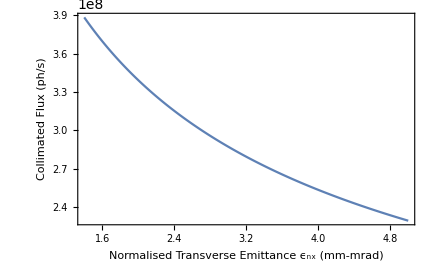

```mathematica
ListLinePlot[ϵvsFψ,Frame->True,FrameLabel->{"Normalised Transverse Emittance ϵ_nx (mm-mrad)","Collimated Flux (ph/s)"},LabelStyle->16]
```

```mathematica
ϵvsΔEγ=Table[{ϵn/(mm mrad),100*ΔEγ[Ee,λ,θcol,ΔEe,Δλ,ϵn,βIP]/.MAXIIIinjopt},{ϵn,ϵn/.MAXIIIinjopt,5 mm mrad, 0.01 mm mrad}];
```

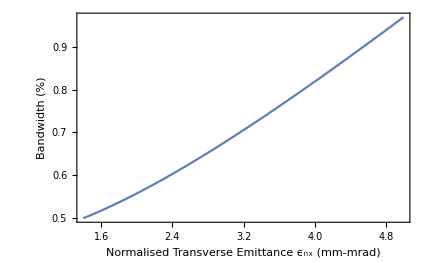

```mathematica
ListLinePlot[ϵvsΔEγ,Frame->True,FrameLabel->{"Normalised Transverse Emittance ϵ_nx (mm-mrad)","Bandwidth (%)"},LabelStyle->16]
```

```mathematica
TwoAxisListPlot[{f_,g_},opts___]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]],opts]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};
fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

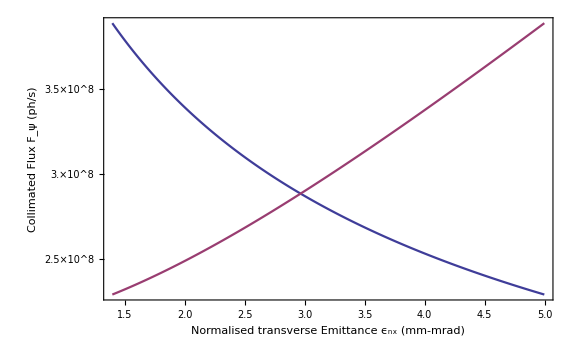

```mathematica
TwoAxisListPlot[{ϵvsFψ,ϵvsΔEγ},{Frame->True,PlotRange->All,Joined->True,ImageSize->Large,FrameLabel->{{"Collimated Flux F_ψ (ph/s)","Bandwidth (%)"},{"Normalised transverse Emittance ϵ_nx (mm-mrad)",""}},BaseStyle->{FontSize->16}}]
```

# Benchmarking - PRAB 20, 080701 (2017)

This is all benchmarking (19) and (20) of PRAB 20, 080701 (2017).

## Serafini Calc Uncollimated

```mathematica
(*Serafini head-on uncollimated flux*)
Nserf[Ee_,λ_,Epulse_,Q_,f_,βIP_,ϵn_,σL_]:=4.2*10^8*(σc[Ee,λ]*Epulse*Q/pC*f)/(σT*EL[λ]*((σe[βIP,ϵn,Ee]/μm)^2+(σL/μm)^2));
```

```mathematica
Nserf[Ee,λ,Epulse,Q,f,βIP,ϵn,σL]/.CBETAopt150headon
```

1.53636×10^11

```mathematica
(*Krafft head-on uncollimated flux*)
Nγ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.CBETAopt150headon
```

Nγ[150000000,133/125000000,1/31250000000,31/500000,0,0.126976,3.×10^-7,1/40000,1/1000,1/100000000000,1.625×10^8]

```mathematica
headfluxdif=(Nserf[Ee,λ,Epulse,Q,f,βIP,ϵn,σL]/.CBETAopt150headon)/(Nγ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.CBETAopt150headon)
```

1.01828

## Serafini Calc Collimated

```mathematica
(*Serafini head-on collimated flux*)
```

```mathematica
Nψserf[Epulse_,Q_,f_,Ee_,λ_,θcol_,βIP_,ϵn_,σL_]:=6.25*10^8*(Epulse*Q/pC*f)/(EL[λ]*((σe[βIP,ϵn,Ee]/μm)^2+(σL/μm)^2))*((1+(CubeRoot[Xrec[Ee,λ]]*ψ[Ee,θcol]^2)/3)*ψ[Ee,θcol]^2)/((1+(1+Xrec[Ee,λ]/2)*ψ[Ee,θcol]^2)*(1+ψ[Ee,θcol]^2));
```

```mathematica
(*Comparison of Serafini, Krafft and my answers to flux in a collimator*)
```

```mathematica
Nψserf[Epulse,Q,f,Ee,λ,θcol,βIP,ϵn,σL]/.CBETAopt150headon
```

3.61933×10^9

```mathematica
Nψ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f,θcol]/.CBETAopt150headon
```

2.38213×10^9

```mathematica
F05[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.CBETAopt150headon
```

1.13093×10^9

```mathematica
(*factors*)
```

```mathematica
mekrafft=(Nψ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f,θcol]/.CBETAopt150headon)/((*headfluxdif*)π*1/Sqrt[2]*F05[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.CBETAopt150headon)
```

0.948189

```mathematica
serfkrafft=(Nψserf[Epulse,Q,f,Ee,λ,θcol,βIP,ϵn,σL]/.CBETAopt150headon)/(headfluxdif*π*F05[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f]/.CBETAopt150headon)
```

1.0004

```mathematica
serfme=(Nψserf[Epulse,Q,f,Ee,λ,θcol,βIP,ϵn,σL]/.CBETAopt150headon)/(headfluxdif*Sqrt[2]*Nψ[Ee,λ,Q,Epulse,ϕ,βIP,ϵn,σL,σze,tpulse,f,θcol]/.CBETAopt150headon)
```

1.05507

Basically we have found that F_(ψ,Krafft) =(√2)/π F_(ψ, Joe). The √2 factor is a mistake I have made in using Serafini’s formula. The π factor is a difference between Serafini’s method and Krafft’s method that I haven’t yet tracked down. I believe the π factor is lost in Eq. (20), the brilliances differ between Krafft and Serafini when Serafini uses N^ψ. The rest can be explained through differences in the spectral shape, as the rough Krafft method assumes this is uniform.